## 3.029 Spring 2022 Assignment 04 Due April 13th at 1pm

## Chemical Phase Diagrams

## General Instructions Reminder

Notebooks should be submitted to canvas

You can choose to submit either a Wolfram Notebook (.nb), or  a Jupyter Notebook (.ipynb)

Please name your notebook using the following notation:
3029__Assignment-04__LASTNAME_FIRSTNAME.nb

Before submitting your notebook:

Make sure all your code runs from a fresh kennel 
Wolfram Notebook: Evaluation → Quit Kernel, Evaluation → Evaluate Notebook
Jupyter Notebook: Kernel → Restart & Run All

Delete all your output
Wolfram Notebook: Cell → Delete All Output
Jupyter Notebook: Cell → All Output → Clear

Tips to maximize your score:

Comment your code well using text cells/Markdown (not in-line comments)

Don’t include extraneous code and narrative that does not contribute to the answer

But feel free to keep a ‘scratch’ notebook as you develop your solutions

Make your graphics are aesthetically pleasing and easy to read

Notably: label your axes and use legible font sizes

## Final Project Proposal (15 points)

Q: Briefly describe your final project idea. This should include the following:

A description of the materials/physics phenomenon you’re trying to model

Relevant computational techniques to model the phenomenon

These need not have been covered in class (although presumably you’re more familiar with those)

Example proposal on the step-growth polymerization we covered in class:

Title: Modeling step-growth polymerization 

Description: Step-growth polymerization is a common polymerization mechanism whereby monomers in solution have reactive end-mers which cause them to form dimers, trimers, longer oligomers, etc. A characteristic of this polymerization mechanism is that high molecular weight polymers require a very high extent of reaction. As such, in addition to dynamic simulations and movies/snapshots of the dynamics, we will evaluate the success of the simulation using plots of the number and weight fractions of the reaction.

Computational Approach: We will model the process in a 2D continuum using polymers with a fixed bond length. 

There are two main parts to the simulation:
	i)	Realistic oligomer motion in solution
	ii)	Oligomer-oligomer collision detection and reaction

For the former, it is common to use Molecular Dynamics for such problems. However, as a learning exercise/coding challenge, we will develop a model for reptation by randomly displacing one monomer on the oligomer chain and "viscously" dragging the other monomers behind it.
For the latter, we will develop a hierarchical collision model (overlapping bounding boxes -> monomers inside overlapping bounding boxes -> pairwise distances b/w remaining monomers) to speed up calculations.

Notes/Open Questions:
- How do we deal with boundary conditions? Periodic? Specular? Diffusive?
- How do we deal with self-loops?
- Speed concerns? Data-size concerns?

Some notes on the level of detail / good aspects of the proposal above

I obviously had the benefit of hindsight in drafting the above, since we've already coded this

I don’t expect you to correctly identify all possible roadblocks at this stage, but it’s a worthwhile exercise to try and speculate

I’ve used an external Wikipedia link to give the reader more information

Adding images also achieves a similar effect

I’ve included a brief description of “figures of merit”

i.e. how will you evaluate your simulation is successful?

I’ve added some notes/open questions at the end  with things I anticipate I will need to address, but not sure yet how/if they’ll end up being a big problem

## Binary Eutectic Phase Diagrams (30 points)

### Solid vs Liquid Phases (5 points)

Recall the “Regular-Activity” (sometimes referred to as the “General”) solution model is given by

```mathematica
molarGibbsEnergy["Regular-Activity"][γA_,γB_,ω_,T_,R_:8.314][xB_]=(1-xB) xB ω+R T ((1-xB) Log[γA(1-xB)]+xB Log[γB xB]);
```

Consider a solid phase using the general solution model above

over the range T ∈ [50,200]

Q: Plot the two molar gibbs free energies for various values of the activities and interaction parameters.
Comment on what the effect of the two modifications are and what their physical origins might be

### Reverse-Engineering a Eutectic Diagram (25 points)

The binary phase diagram of the Orthoclase (K Al Si_3 O_8) - Albite (Na Al Si_3 O_8) system demonstrates a nice transition between a liquidus minimum + miscibility gap to a eutectic diagram

-Graphics-

Q: Using the solid- and liquid-phase molar Gibbs free energy forms above reproduce the following phase-diagram features:
Notes:	1. The `phaseDiagramExplorer` and `phaseDiagram` functions  from L15 are summarized below in the initialization cells for convenience)
		As a reminder, these are called as `phaseDiagram[listOfPhase(s),{50,200,1}]` and `phaseDiagramExplorer[listOfPhase(s),{50,200,1}]`
	2. An example solution is given for each. Yours will likely look different, that’s ok - there are many activities/interaction parameter choices to achieve the desired result
	3. Make sure to comment on your results!

A solid-solution miscibility gap

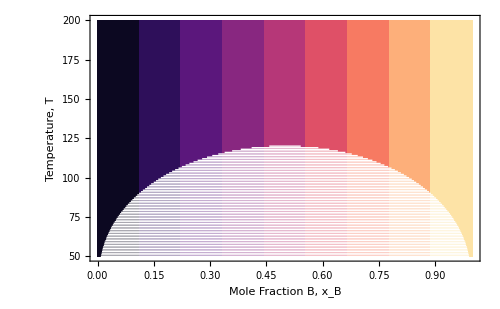

A liquidus minimum

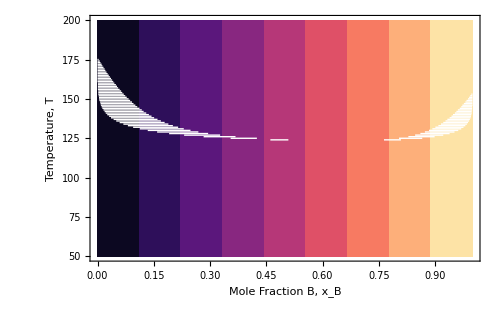

A liquidus minimum + miscibility gap

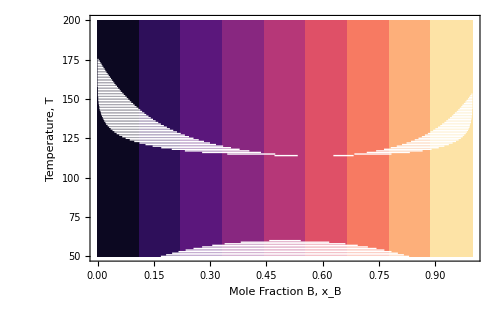

A eutectic diagram

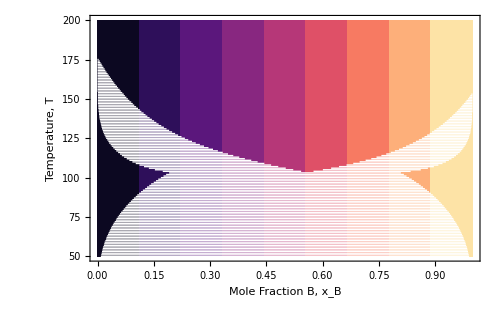

Identify the eutectic temperature and composition

#### Binary Phase Diagram Initialization Code

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
```

```mathematica
minimumPoints[functionList_, numPts_] :=Thread[{Subdivide[numPts],Min/@Thread[Through[functionList[Subdivide[numPts]]]]}]

getConvexHullVertices[candidatePoints_] := Module[{
maxY = Max[Last /@ candidatePoints],
amendedPoints
}, 
amendedPoints = Join[{{0., 1 + maxY}}, candidatePoints, {{1., 1 + maxY}}]; 
MeshCoordinates[ConvexHullMesh[amendedPoints]][[2;;-2]]
]
```

```mathematica
backgroundGraphic[Tmin_,Tmax_]:=backgroundGraphic[Tmin,Tmax]=DensityPlot[x,{x,0,1},{y,Tmin,Tmax},ColorFunction->MPLColorMap["Magma"]][[1]]
```

```mathematica
freeEnergyLineGraphicAndMiscibilityGaps[functionList_,numPts_] := 
Module[{convexHullPoints = getConvexHullVertices[minimumPoints[functionList, numPts]],
singlePhasePoints,miscibilityGaps,cf=MPLColorMap["Magma"],cols},
singlePhasePoints=Split[convexHullPoints,First[#2]-First[#1]<1.001/numPts&];
miscibilityGaps={Last[#1],First[#2]}&@@@Partition[singlePhasePoints,2,1];
cols=Map[cf[First[#]]&,singlePhasePoints,{2}];

{Graphics[{Thick,MapThread[Line[#1,VertexColors->#2]&,{singlePhasePoints,cols}],Black,Dotted,Line/@miscibilityGaps}],miscibilityGaps}
]
```

```mathematica
showTieLines[{Tmin_,Tmax_,ΔT_}][tieLines_,temperature_]:=Graphics[{
backgroundGraphic[Tmin,Tmax],
{White,Values[tieLines]},
{LightGray,Line[{{0,temperature},{1,temperature}}]}
},PlotRange->{{0,1},{Tmin,Tmax}},FrameLabel->{"Mole Fraction B, x_B","Temperature, T"},Frame->True,PlotRangeClipping->True,ImageSize->500,LabelStyle->Directive[Black,16],ImagePadding->{{75,15},{50,15}},AspectRatio->1/GoldenRatio]
```

```mathematica
showFreeEnergyGraphicAndReturnMiscibilityGaps[functionList_,temperature_,numPts_]:=Block[{fs=Through[functionList[temperature]],graphic,tieline},
{graphic,tieline}=freeEnergyLineGraphicAndMiscibilityGaps[fs,numPts];
graphic=Show[Plot[Through[fs[xB]],{xB,0,1},PlotStyle->LightGray,Frame->True,LabelStyle->Directive[Black,16],ImageSize->500,ImagePadding->{{75,15},{50,15}},FrameLabel->{"Mole Fraction B, x_B","Molar Gibbs Energy, G̲"}],graphic];
{graphic,tieline}
]
```

```mathematica
phaseDiagramExplorer[functionList_,{Tmin_,Tmax_,ΔT_}, numPts_]:= 
DynamicModule[{
tieLines = <||>,allTemperatures,meanTemperature,showFreeEnergyAndPhaseDiagramGraphic
},

allTemperatures = Range[Tmin, Tmax, ΔT];
meanTemperature = allTemperatures[[Round[Length[allTemperatures]/2]]];

showFreeEnergyAndPhaseDiagramGraphic[temperature_]:=Block[{graphic,tieline},
If[KeyExistsQ[tieLines,temperature],

Column[{
showFreeEnergyGraphicAndReturnMiscibilityGaps[functionList,temperature,numPts]//First,
showTieLines[{Tmin,Tmax,ΔT}][tieLines,temperature]}
],

{graphic,tieline}=showFreeEnergyGraphicAndReturnMiscibilityGaps[functionList,temperature,numPts];
AssociateTo[tieLines,temperature->Line/@Map[Thread[{#,temperature}]&,tieline[[All,All,1]],{2}]];
Column[{graphic,showTieLines[{Tmin,Tmax,ΔT}][tieLines,temperature]}]
]
];

Manipulate[
If[computeAll && Length[tieLines] < Length[allTemperatures], 
 temperature= First[Sort[Complement[allTemperatures, Keys[tieLines]]]]];

If[Length[tieLines]≥ Length[allTemperatures], computeAll=False];

showFreeEnergyAndPhaseDiagramGraphic[temperature],

{{temperature,meanTemperature,Style["Temperature",FontSize->12]},allTemperatures,Slider},
Delimiter,
{{computeAll,False,Style["Compute all tie-lines",FontSize->12]},{False, True}},Paneled->False
]
]
```

```mathematica
miscibilityGaps[functionList_,temperature_,numPts_] :=
Module[{convexHullPoints = getConvexHullVertices[minimumPoints[Through[functionList[temperature]], numPts]],singlePhasePoints,miscibilityGaps,cf=MPLColorMap["Magma"],cols},
singlePhasePoints=Split[convexHullPoints,First[#2]-First[#1]<1.001/numPts&];
miscibilityGaps={Last[#1],First[#2]}&@@@Partition[singlePhasePoints,2,1];
Line/@Map[Thread[{#,temperature}]&,miscibilityGaps[[All,All,1]],{2}]
]
```

```mathematica
phaseDiagram[functionList_,{Tmin_,Tmax_,ΔT_},Δx_:1/1000]:=
Block[{numPts=Round[1/Δx],bckg=backgroundGraphic[Tmin,Tmax],Ts=Range[Tmin,Tmax,ΔT],tieLines},

tieLines=Monitor[Table[miscibilityGaps[functionList,Ts[[T]],numPts],{T,Length[Ts]}],ProgressIndicator[T,{1,Length[Ts]}]];

Graphics[{bckg,White,tieLines},PlotRange->{{0,1},{Tmin,Tmax}},FrameLabel->{"Mole Fraction B, x_B","Temperature, T"},Frame->True,PlotRangeClipping->True,ImageSize->500,LabelStyle->Directive[Black,16],ImagePadding->{{75,15},{50,15}},AspectRatio->1/GoldenRatio]
]
```

## Ternary Solidification (25 points)

### Liquidus Projection (10 points)

Consider the following ternary liquidus surface
Note: this is constructed geometrically in the initialization cells below. No need to understand where this form came from - it’s not very physical.

The initialization function returns a grid of liquidus points with the form {x_G,y_G,T}

where x_G and y_G are the coordinates inside the Gibbs triangle (remember: these are not the compositions x_A,x_B) and the liquidus temperature at that point

```mathematica
Short[liquidusPoints=ternaryLiquidusSurface[0.5,0.625,0.75]]
```

{{0.246577,0.425914,0.551887},«16790»,{0.251977,0.00900732,0.431771}}

This is called the ‘space model’ for ternary phase diagrams, and can be plotted as follows

```mathematica
With[{liquidusPoints=ternaryLiquidusSurface[0.5,0.625,0.75]},
Show[
ListSurfacePlot3D[liquidusPoints,MaxPlotPoints->100,RegionFunction->Function[{x,y,z},gibbsRegionMember[{x,y}]],Boxed->False,Axes->False,MeshFunctions->(#3&),ColorFunction->Function[{x,y,z},ColorData["TemperatureMap"][z]]],gibbsPrismGraphics,ViewPoint->{1, -1, 1}]
]
```

-Graphics3D-

The same information can be displayed by projecting the temperature-axis on the basal plane

This is called the liquidus projection

Q: Plot the liquidus projection of the ternary surface above and clearly label all components.
Is there an equivalent solidus projection?

### Solidification (10 points)

Q: Consider starting at composition x_A=0.15, x_B=0.1, x_C=0.75 at a temperature above the liquidus surface, and slowly start decreasing the temperature. 
Describe the solidification process.

Note: You shouldn’t need to calculate anything for this. Describe the phase separation qualitatively (possibly with the aid of some diagrams)

### Isopleth Diagrams (5 points)

We can also fix one of the compositions, and plot this as a binary system

This is called an isopleth diagram

Q: Plot isopleth diagrams of the liquidus surface for the following fixed x_C concentrations:

x_C=0.0, 0.1,0.2,0.3, 0.4 ,0.5,0.6 ,0.7 ,0.8 ,0.9

#### Liquidus Initialization Code

```mathematica
gibbsTriangle=SSSTriangle[1,1,1];
gibbsPrism=RegionProduct[gibbsTriangle,Line[{{0},{1}}]];
gibbsRegionMember=RegionMember[TransformedRegion[gibbsTriangle,ScalingTransform[{0.9999,0.9999},RegionCentroid[gibbsTriangle]]]];

gibbsPrismGraphics=Graphics3D[{EdgeForm[Black],FaceForm[None],gibbsPrism,FaceForm[Red],GeometricTransformation[MapThread[Text[Style[#1,18],#2]&,{{"A","B","C"},Flatten/@Thread[{gibbsTriangle[[1]],0}]}],ScalingTransform[{1.15,1.15,1},Append[RegionCentroid[gibbsTriangle],0]]]}];

ternaryLiquidusGeometric[r1_,r2_,r3_]:=RegionIntersection[
RegionUnion@@MapThread[Ball,{Flatten/@Thread[{gibbsTriangle[[1]],0}],{r1,r2,r3}}],
gibbsPrism
]

Needs["NDSolve`FEM`"]
Clear[ternaryLiquidusSurface]
ternaryLiquidusSurface[r1_,r2_,r3_]:=ternaryLiquidusSurface[r1,r2,r3]=Block[{bmesh,rm=gibbsRegionMember},
bmesh=ToBoundaryMesh[ternaryLiquidusGeometric[r1,r2,r3],"MaxBoundaryCellMeasure"->.0001];
Select[bmesh["Coordinates"],rm[Most[#]]&&Last[#]>0&]
]
```

## Multicomponent Systems (30 points)

### Multi-component Regular-Activity model (5 points)

The Regular-Activity model can be generalized to multi-component systems as

where m is the number of components, ω_ij are interaction parameters between components i-j, and γ_i is the activity coefficient of the i^th component

Q: write two functions to express the regular-activity model for ternary and quaternary systems.

Hint: you may find this xlogx function useful

```mathematica
Clear[xlogx]
xlogx[x_,γ_:1]=x Log[γ x];
xlogx[0,γ_:1]=xlogx[0.0,γ_:1]=0.0;
xlogx[1,γ_:1]=xlogx[1.0,γ_:1]=Log[γ];
```

Q: Plot the ternary regular-activity solution model on the Gibbs triangle for various interaction parameters and temperatures

### Quaternary Plot (10 points)

Q: Generalize the gibbs triangle construction we used for the ternary triangle for the quaternary case

Q: Plot the quaternary regular-activity solution model on your generalization of the Gibbs triangle above  for various interaction parameters and temperatures

Hint: Use color to represent the value of the molar Gibbs free energy

### Ternary Level Rule (15 points)

Recall the ternary phase diagram we saw in L16, with three 3-phase regions

```mathematica
ternaryPhase["A"][xa_,xb_]:=With[{xc=1-xa-xb},100(xa^2 xb^2 xc^2 +(xlogx[xa] + xlogx[xb] + xlogx[xc])/1000)];

ternaryPhase["B"][xa_,xb_]:=With[{xc=1-xa-xb},.01-.125Exp[-25((xa-(1/2-1/(2 √3)))^2 + (xb-1/(√3))^2 +(xc-(1/2-1/(2 √3)))^2)]];

ternaryPhaseDiagram[{ternaryPhase["A"],ternaryPhase["B"]},False,150]
```

-Graphics-

The “B-rich” three-phase region can be extracted as follows

```mathematica
threePhaseRegion=Last[getConvexHullPolygons3D[minimumPoints3D[{ternaryPhase["A"],ternaryPhase["B"]},150],150]][[3,All,;;2]]
```

{{0.746667,0.213333},{0.746667,0.04},{0.22,0.573333}}

Note the points above refer to the (x_A,x_B) compositions of the three vertices.
I.e. if you wanted to see this in the GIbbs triangle, you would need to use the transformation function we introduced in L16

```mathematica
Graphics[{EdgeForm[Black],FaceForm[None],SSSTriangle[1,1,1],FaceForm[Red],GeometricTransformation[Polygon[threePhaseRegion],transformationFunction]}]
```

-Graphics-

Q: Using the geometrical constructions we showed in L16, generalize the level rule to arbitrary three phase regions

Q: Use for generalized lever rule above to specify the phase fractions of the three co-existing compositions at the following requested compositions
Note: these are again given as (x_A,x_B)

```mathematica
SeedRandom[11];
compositions=RandomPoint[Polygon[threePhaseRegion],3]

Graphics[{EdgeForm[Black],FaceForm[None],SSSTriangle[1,1,1],FaceForm[Red],GeometricTransformation[{Polygon[threePhaseRegion],PointSize[Large],Point[compositions]},transformationFunction]}]
```

{{0.670053,0.143344},{0.56552,0.328982},{0.640373,0.234234}}

-Graphics-

#### Ternary Phase Diagram Initialization Code

```mathematica
transformationFunction={{1,1/2},{0,(√3)/2}};

minimumPoints3D[functionList_, numPts_] :=With[{
pts=Select[Join@@Table[{xA,xB},{xA,Subdivide[numPts]},{xB,Subdivide[numPts]}],Total[#]<= 1&]},
N[Append[#,Min[Through[functionList@@#]]]&/@pts]
]

triangleArea[pts:{{p1x_,p1y_},{p2x_,p2y_},{p3x_,p3y_}}]=Area[Triangle[{{p1x,p1y},{p2x,p2y},{p3x,p3y}}]];

splitSinglePhaseRegions[singlePhaseRegion_MeshRegion]:=Block[{rms,coords,polys,polysSplit},
coords=MeshCoordinates[singlePhaseRegion];
polys=MeshCells[singlePhaseRegion,2];

If[First[Nearest[coords[[All,;;2]]->"Distance",{0.,0.}]]>10^-6,Return[{Extract[coords,List@*First/@polys]}]];

rms=RegionMember@*Polygon/@Rest[Subsets[Append[First[TransformedRegion[Triangle[],ScalingTransform[{4/3,4/3},{1/3,1/3}]]],{1/3,1/3}],{3}]];
polysSplit=GatherBy[polys,Last[Ordering[Boole[Through[rms[coords[[First[#],;;2]]]]],-1,Total[#1]<Total[#2]&]]&];
Extract[coords,List@*First/@#]&/@polysSplit
]

splitTwoPhaseRegions[twoPhaseRegions_]:=Block[{groupByLength,triangles,quads,triangleLines,quadLines},

groupByLength=GroupBy[twoPhaseRegions,Length];

triangles=groupByLength[3];
triangleLines=If[MissingQ[triangles],{},
First[MaximalBy[TriangleConstruct[#[[All,;;2]],{"AngleBisectingCevian",All}],RegionMeasure]]&/@triangles];

quads=groupByLength[4];
quadLines=If[MissingQ[quads],{},
Line/@Partition[#[[All,;;2]],2,1]&/@quads];

Join[triangleLines,quadLines]
]

getConvexHullPolygons3D[candidatePoints_,numPts_] := Module[{
maxZ = Max[Last/@candidatePoints],area=(1/numPts)^2,
amendedPoints,ch,pts,polygonIndices,groupedLength,singlePhaseRegionPositions,singlePhaseRegion,singlePhaseRegions,twoPlusPhaseRegions,clusteredRegions,rms,groupByCoexistence
}, 

amendedPoints = Join[{{0., 0.,1 + maxZ}}, candidatePoints, {{1.,0., 1 + maxZ},{0.,1., 1 + maxZ}}]; 
ch=ConvexHullMesh[amendedPoints];
pts=MeshCoordinates[ch];
polygonIndices=MeshCells[ch,2];
polygonIndices=Select[polygonIndices,And@@Thread[pts[[First[#],3]]<=maxZ]&];
groupedLength=GroupBy[polygonIndices,Length@*First];
singlePhaseRegionPositions=Position[groupedLength[3],Polygon[{a_,b_,c_}]/;triangleArea[pts[[{a,b,c},;;2]]]<area];
singlePhaseRegion=Extract[groupedLength[3],singlePhaseRegionPositions];

twoPlusPhaseRegions=Flatten[{Values[KeyDrop[groupedLength,3]],Delete[groupedLength[3],singlePhaseRegionPositions]}];
twoPlusPhaseRegions=Extract[pts,List@*First/@twoPlusPhaseRegions];

singlePhaseRegions=ConnectedMeshComponents[MeshRegion[pts,singlePhaseRegion]];
clusteredRegions=Join@@(splitSinglePhaseRegions/@singlePhaseRegions);

rms=RegionMember@*Polygon/@clusteredRegions;
groupByCoexistence=GroupBy[twoPlusPhaseRegions,Length[Position[Unitize[Total/@Boole[Through[rms[#]]]],1]]&];

{Join@@clusteredRegions,groupByCoexistence[2],groupByCoexistence[3]}

]

concToColor[{xA_,xB_,g_}]:=RGBColor[xA,xB,1-xA-xB]

colorTernaryPhaseDiagram[{singlePhaseRegions_,twoPhaseRegions_,threePhaseRegions_},showTieLines_:False,labels_:{"A","B","C"}]:=
Block[{singlePhaseCols=Map[concToColor,singlePhaseRegions,{2}],graphicsObject,labelCoords},
labelCoords=First[TransformedRegion[SSSTriangle[1,1,1],ScalingTransform[{19/18,19/18},{1/2,1/(2 √3)}]]];
graphicsObject=MapThread[Polygon[#1[[All,;;2]],VertexColors->#2]&,{singlePhaseRegions,singlePhaseCols}];

graphicsObject=Join[graphicsObject,{PatternFilling[{"DiamondPlate",LightGray},ImageScaled[0.025]],Polygon/@threePhaseRegions[[All,All,;;2]]}];

graphicsObject=If[showTieLines,
Join[graphicsObject,{Black,Thin,splitTwoPhaseRegions[twoPhaseRegions]}],
Join[graphicsObject,{PatternFilling[{"Halftone",Black},ImageScaled[0.025]],Polygon/@twoPhaseRegions[[All,All,;;2]]}]];

Graphics[{EdgeForm[None],GeometricTransformation[graphicsObject,transformationFunction],MapThread[Text[#1,#2,BaseStyle->24]&,{labels,labelCoords}]},ImageSize->500]
]

ternaryPhaseDiagram[functionList_,showTieLines_:False,numPts_:100,labels_:{"A","B","C"}]:=Rasterize[colorTernaryPhaseDiagram[getConvexHullPolygons3D[minimumPoints3D[functionList,numPts],numPts],showTieLines,labels],RasterSize->1000,ImageSize->500]
```